```mathematica
A=1
J=2.5
J001=Table[u/.FindRoot[A×x^-1.5×ⅇ^(-J×x)×∑_(l=1)^Num l^1.5×ⅇ^(-u×l)-1,{u,-0.001}],{Num,10000,40000,5000},{x,0.01,15,0.1}]
```

1

2.5

{{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145774,0.00130508,0.00116855,0.00104635,0.000936798,0.000838352,0.000749576,0.000669149,0.000595876,0.000528698,0.000466689,0.000409058,0.000355133,0.00030435,0.000256238,0.000210406,0.000166524,0.000124322,0.0000835689,0.000044075,5.67865×10^-6,-0.0000317564,-0.0000683458,-0.000104188,-0.000139367,-0.000173955,-0.000208014,-0.000241599,-0.000274755,-0.000307525,-0.000339944,-0.000372043,-0.000403849,-0.000435387,-0.00046668,-0.000497745,-0.0005286,-0.000559261,-0.000589741,-0.000620053,-0.000650208,-0.000680216,-0.000710086,-0.000739827,-0.000769446,-0.00079895,-0.000828345,-0.000857638,-0.000886834,-0.000915937,-0.000944953,-0.000973885,-0.00100274,-0.00103151,-0.00106022,-0.00108885,-0.00111742,-0.00114592,-0.00117437,-0.00120275,-0.00123108,-0.00125935,-0.00128757,-0.00131574,-0.00134386,-0.00137194,-0.00139997,-0.00142795,-0.00145589,-0.0014838,-0.00151166,-0.00153948,-0.00156727,-0.00159501,-0.00162273,-0.00165041,-0.00167805,-0.00170567,-0.00173325,-0.0017608,-0.00178832,-0.00181581,-0.00184328,-0.00187071,-0.00189812,-0.00192551,-0.00195286,-0.00198019,-0.0020075,-0.00203479,-0.00206205,-0.00208928,-0.0021165,-0.00214369},{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145776,0.00130512,0.00116869,0.0010467,0.000937592,0.000839979,0.000752593,0.000674283,0.000603983,0.000540707,0.000483535,0.000431628,0.000384229,0.000340667,0.000300362,0.000262815,0.000227607,0.000194385,0.000162854,0.000132767,0.000103919,0.0000761396,0.0000492839,0.0000232316,-2.11925×10^-6,-0.0000268547,-0.0000510479,-0.0000747615,-0.0000980489,-0.000120956,-0.000143523,-0.000165784,-0.000187768,-0.000209503,-0.000231011,-0.000252312,-0.000273423,-0.000294361,-0.000315139,-0.00033577,-0.000356265,-0.000376634,-0.000396886,-0.000417028,-0.000437068,-0.000457012,-0.000476867,-0.000496638,-0.000516329,-0.000535946,-0.000555492,-0.000574971,-0.000594387,-0.000613743,-0.000633042,-0.000652286,-0.000671478,-0.000690621,-0.000709716,-0.000728766,-0.000747773,-0.000766738,-0.000785663,-0.00080455,-0.0008234,-0.000842215,-0.000860995,-0.000879743,-0.000898459,-0.000917144,-0.000935799,-0.000954426,-0.000973025,-0.000991597,-0.00101014,-0.00102866,-0.00104716,-0.00106563,-0.00108408,-0.00110251,-0.00112091,-0.0011393,-0.00115766,-0.00117601,-0.00119433,-0.00121263,-0.00123092,-0.00124919,-0.00126744,-0.00128567,-0.00130389,-0.00132209,-0.00134028,-0.00135844},{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145776,0.00130512,0.00116869,0.0010467,0.000937605,0.000840021,0.000752711,0.000674573,0.000604613,0.000541931,0.000485701,0.000435156,0.000389584,0.000348324,0.000310776,0.0002764,0.000244723,0.000215335,0.000187888,0.000162089,0.000137689,0.000114484,0.0000923004,0.0000709956,0.000050449,0.0000305599,0.0000112432,-7.5726×10^-6,-0.0000259483,-0.0000439358,-0.0000615791,-0.0000789163,-0.0000959799,-0.000112798,-0.000129396,-0.000145795,-0.000162012,-0.000178066,-0.000193969,-0.000209735,-0.000225376,-0.0002409,-0.000256317,-0.000271636,-0.000286862,-0.000302003,-0.000317064,-0.000332051,-0.000346968,-0.00036182,-0.00037661,-0.000391342,-0.00040602,-0.000420645,-0.000435222,-0.000449753,-0.00046424,-0.000478684,-0.000493089,-0.000507456,-0.000521786,-0.000536082,-0.000550344,-0.000564575,-0.000578775,-0.000592946,-0.000607089,-0.000621204,-0.000635294,-0.000649358,-0.000663399,-0.000677415,-0.00069141,-0.000705382,-0.000719334,-0.000733265,-0.000747176,-0.000761068,-0.000774942,-0.000788797,-0.000802635,-0.000816457,-0.000830261,-0.00084405,-0.000857823,-0.000871581,-0.000885324,-0.000899053,-0.000912767,-0.000926468,-0.000940156,-0.000953831,-0.000967493,-0.000981143},{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145776,0.00130512,0.00116869,0.0010467,0.000937605,0.000840022,0.000752715,0.000674587,0.000604658,0.00054205,0.000485975,0.000435718,0.00039062,0.000350074,0.000313511,0.000280407,0.000250281,0.000222704,0.000197295,0.000173728,0.000151722,0.000131042,0.000111489,0.0000928973,0.0000751283,0.0000580666,0.0000416152,0.0000256929,0.0000102314,-4.82698×10^-6,-0.0000195313,-0.0000339233,-0.0000480386,-0.0000619077,-0.0000755569,-0.000089009,-0.000102284,-0.000115398,-0.000128368,-0.000141206,-0.000153923,-0.00016653,-0.000179036,-0.000191449,-0.000203777,-0.000216025,-0.000228199,-0.000240305,-0.000252347,-0.000264329,-0.000276256,-0.00028813,-0.000299955,-0.000311734,-0.000323469,-0.000335163,-0.000346817,-0.000358435,-0.000370017,-0.000381566,-0.000393083,-0.00040457,-0.000416027,-0.000427457,-0.000438861,-0.000450239,-0.000461592,-0.000472923,-0.000484231,-0.000495517,-0.000506782,-0.000518028,-0.000529254,-0.000540462,-0.000551651,-0.000562823,-0.000573979,-0.000585118,-0.000596241,-0.00060735,-0.000618443,-0.000629522,-0.000640587,-0.000651639,-0.000662677,-0.000673703,-0.000684716,-0.000695718,-0.000706707,-0.000717685,-0.000728652,-0.000739608,-0.000750554,-0.000761489},{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145776,0.00130512,0.00116869,0.0010467,0.000937605,0.000840022,0.000752715,0.000674588,0.000604661,0.000542061,0.000486008,0.000435803,0.000390816,0.000350472,0.000314242,0.000281631,0.000252183,0.000225474,0.00020112,0.000178776,0.000158144,0.000138963,0.000121015,0.000104112,0.0000881012,0.0000728506,0.0000582523,0.0000442153,0.0000306635,0.000017533,4.7699×10^-6,-7.67133×10^-6,-0.0000198294,-0.0000317374,-0.0000434235,-0.0000549119,-0.0000662236,-0.0000773767,-0.000088387,-0.000099268,-0.000110032,-0.000120689,-0.000131249,-0.00014172,-0.000152109,-0.000162423,-0.000172667,-0.000182846,-0.000192966,-0.00020303,-0.000213042,-0.000223006,-0.000232924,-0.000242799,-0.000252635,-0.000262432,-0.000272194,-0.000281922,-0.000291618,-0.000301284,-0.000310921,-0.000320531,-0.000330115,-0.000339674,-0.000349209,-0.000358721,-0.000368212,-0.000377682,-0.000387132,-0.000396563,-0.000405976,-0.00041537,-0.000424748,-0.000434109,-0.000443455,-0.000452785,-0.000462101,-0.000471402,-0.000480689,-0.000489963,-0.000499224,-0.000508473,-0.00051771,-0.000526934,-0.000536148,-0.00054535,-0.000554541,-0.000563722,-0.000572893,-0.000582054,-0.000591205,-0.000600347,-0.000609479,-0.000618603},{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145776,0.00130512,0.00116869,0.0010467,0.000937605,0.000840022,0.000752715,0.000674588,0.000604661,0.000542062,0.000486012,0.000435816,0.000390852,0.000350561,0.000314433,0.000282004,0.000252841,0.00022654,0.000202728,0.000181063,0.000161237,0.000142978,0.00012605,0.000110253,0.0000954139,0.0000813911,0.0000680643,0.0000553333,0.0000431141,0.0000313366,0.000019942,8.88074×10^-6,-1.88913×10^-6,-0.0000124031,-0.0000226913,-0.0000327797,-0.0000426904,-0.0000524424,-0.0000620522,-0.0000715342,-0.0000809008,-0.0000901629,-0.0000993299,-0.00010841,-0.000117412,-0.00012634,-0.000135202,-0.000144002,-0.000152746,-0.000161436,-0.000170077,-0.000178673,-0.000187226,-0.000195738,-0.000204214,-0.000212654,-0.000221061,-0.000229437,-0.000237783,-0.000246101,-0.000254393,-0.000262659,-0.000270902,-0.000279122,-0.00028732,-0.000295498,-0.000303656,-0.000311795,-0.000319916,-0.000328019,-0.000336106,-0.000344177,-0.000352232,-0.000360273,-0.0003683,-0.000376313,-0.000384312,-0.000392299,-0.000400273,-0.000408236,-0.000416187,-0.000424126,-0.000432055,-0.000439974,-0.000447882,-0.00045578,-0.000463669,-0.000471548,-0.000479419,-0.00048728,-0.000495133,-0.000502978,-0.000510815,-0.000518643},{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145776,0.00130512,0.00116869,0.0010467,0.000937605,0.000840022,0.000752715,0.000674588,0.000604661,0.000542062,0.000486012,0.000435818,0.000390858,0.00035058,0.000314483,0.000282116,0.000253067,0.000226951,0.000203412,0.00018212,0.000162768,0.000145082,0.000128816,0.000113759,0.0000997282,0.0000865678,0.0000741478,0.0000623591,0.0000511102,0.0000403249,0.0000299393,0.0000198997,0.0000101611,6.85398×10^-7,-8.55965×10^-6,-0.0000176015,-0.0000264635,-0.0000351658,-0.0000437257,-0.0000521581,-0.0000604758,-0.0000686902,-0.0000768111,-0.0000848471,-0.0000928057,-0.000100694,-0.000108517,-0.00011628,-0.000123989,-0.000131647,-0.000139258,-0.000146825,-0.000154352,-0.000161841,-0.000169294,-0.000176714,-0.000184103,-0.000191462,-0.000198794,-0.0002061,-0.000213381,-0.000220638,-0.000227873,-0.000235088,-0.000242282,-0.000249457,-0.000256613,-0.000263753,-0.000270875,-0.000277982,-0.000285073,-0.00029215,-0.000299213,-0.000306262,-0.000313298,-0.000320322,-0.000327333,-0.000334333,-0.000341321,-0.000348299,-0.000355266,-0.000362224,-0.000369171,-0.000376109,-0.000383037,-0.000389957,-0.000396868,-0.00040377,-0.000410664,-0.000417551,-0.000424429,-0.0004313,-0.000438164,-0.000445021}}

```mathematica
Length[J001]
```

7

```mathematica
J05 = J001[[1]]
J1 = J001[[2]]
J105 = J001[[3]]
J2=J001[[4]]
J205 = J001[[5]]
J3 = J001[[6]]
J305 = J001[[7]]
```

{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145774,0.00130508,0.00116855,0.00104635,0.000936798,0.000838352,0.000749576,0.000669149,0.000595876,0.000528698,0.000466689,0.000409058,0.000355133,0.00030435,0.000256238,0.000210406,0.000166524,0.000124322,0.0000835689,0.000044075,5.67865×10^-6,-0.0000317564,-0.0000683458,-0.000104188,-0.000139367,-0.000173955,-0.000208014,-0.000241599,-0.000274755,-0.000307525,-0.000339944,-0.000372043,-0.000403849,-0.000435387,-0.00046668,-0.000497745,-0.0005286,-0.000559261,-0.000589741,-0.000620053,-0.000650208,-0.000680216,-0.000710086,-0.000739827,-0.000769446,-0.00079895,-0.000828345,-0.000857638,-0.000886834,-0.000915937,-0.000944953,-0.000973885,-0.00100274,-0.00103151,-0.00106022,-0.00108885,-0.00111742,-0.00114592,-0.00117437,-0.00120275,-0.00123108,-0.00125935,-0.00128757,-0.00131574,-0.00134386,-0.00137194,-0.00139997,-0.00142795,-0.00145589,-0.0014838,-0.00151166,-0.00153948,-0.00156727,-0.00159501,-0.00162273,-0.00165041,-0.00167805,-0.00170567,-0.00173325,-0.0017608,-0.00178832,-0.00181581,-0.00184328,-0.00187071,-0.00189812,-0.00192551,-0.00195286,-0.00198019,-0.0020075,-0.00203479,-0.00206205,-0.00208928,-0.0021165,-0.00214369}

{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145776,0.00130512,0.00116869,0.0010467,0.000937592,0.000839979,0.000752593,0.000674283,0.000603983,0.000540707,0.000483535,0.000431628,0.000384229,0.000340667,0.000300362,0.000262815,0.000227607,0.000194385,0.000162854,0.000132767,0.000103919,0.0000761396,0.0000492839,0.0000232316,-2.11925×10^-6,-0.0000268547,-0.0000510479,-0.0000747615,-0.0000980489,-0.000120956,-0.000143523,-0.000165784,-0.000187768,-0.000209503,-0.000231011,-0.000252312,-0.000273423,-0.000294361,-0.000315139,-0.00033577,-0.000356265,-0.000376634,-0.000396886,-0.000417028,-0.000437068,-0.000457012,-0.000476867,-0.000496638,-0.000516329,-0.000535946,-0.000555492,-0.000574971,-0.000594387,-0.000613743,-0.000633042,-0.000652286,-0.000671478,-0.000690621,-0.000709716,-0.000728766,-0.000747773,-0.000766738,-0.000785663,-0.00080455,-0.0008234,-0.000842215,-0.000860995,-0.000879743,-0.000898459,-0.000917144,-0.000935799,-0.000954426,-0.000973025,-0.000991597,-0.00101014,-0.00102866,-0.00104716,-0.00106563,-0.00108408,-0.00110251,-0.00112091,-0.0011393,-0.00115766,-0.00117601,-0.00119433,-0.00121263,-0.00123092,-0.00124919,-0.00126744,-0.00128567,-0.00130389,-0.00132209,-0.00134028,-0.00135844}

{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145776,0.00130512,0.00116869,0.0010467,0.000937605,0.000840021,0.000752711,0.000674573,0.000604613,0.000541931,0.000485701,0.000435156,0.000389584,0.000348324,0.000310776,0.0002764,0.000244723,0.000215335,0.000187888,0.000162089,0.000137689,0.000114484,0.0000923004,0.0000709956,0.000050449,0.0000305599,0.0000112432,-7.5726×10^-6,-0.0000259483,-0.0000439358,-0.0000615791,-0.0000789163,-0.0000959799,-0.000112798,-0.000129396,-0.000145795,-0.000162012,-0.000178066,-0.000193969,-0.000209735,-0.000225376,-0.0002409,-0.000256317,-0.000271636,-0.000286862,-0.000302003,-0.000317064,-0.000332051,-0.000346968,-0.00036182,-0.00037661,-0.000391342,-0.00040602,-0.000420645,-0.000435222,-0.000449753,-0.00046424,-0.000478684,-0.000493089,-0.000507456,-0.000521786,-0.000536082,-0.000550344,-0.000564575,-0.000578775,-0.000592946,-0.000607089,-0.000621204,-0.000635294,-0.000649358,-0.000663399,-0.000677415,-0.00069141,-0.000705382,-0.000719334,-0.000733265,-0.000747176,-0.000761068,-0.000774942,-0.000788797,-0.000802635,-0.000816457,-0.000830261,-0.00084405,-0.000857823,-0.000871581,-0.000885324,-0.000899053,-0.000912767,-0.000926468,-0.000940156,-0.000953831,-0.000967493,-0.000981143}

{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145776,0.00130512,0.00116869,0.0010467,0.000937605,0.000840022,0.000752715,0.000674587,0.000604658,0.00054205,0.000485975,0.000435718,0.00039062,0.000350074,0.000313511,0.000280407,0.000250281,0.000222704,0.000197295,0.000173728,0.000151722,0.000131042,0.000111489,0.0000928973,0.0000751283,0.0000580666,0.0000416152,0.0000256929,0.0000102314,-4.82698×10^-6,-0.0000195313,-0.0000339233,-0.0000480386,-0.0000619077,-0.0000755569,-0.000089009,-0.000102284,-0.000115398,-0.000128368,-0.000141206,-0.000153923,-0.00016653,-0.000179036,-0.000191449,-0.000203777,-0.000216025,-0.000228199,-0.000240305,-0.000252347,-0.000264329,-0.000276256,-0.00028813,-0.000299955,-0.000311734,-0.000323469,-0.000335163,-0.000346817,-0.000358435,-0.000370017,-0.000381566,-0.000393083,-0.00040457,-0.000416027,-0.000427457,-0.000438861,-0.000450239,-0.000461592,-0.000472923,-0.000484231,-0.000495517,-0.000506782,-0.000518028,-0.000529254,-0.000540462,-0.000551651,-0.000562823,-0.000573979,-0.000585118,-0.000596241,-0.00060735,-0.000618443,-0.000629522,-0.000640587,-0.000651639,-0.000662677,-0.000673703,-0.000684716,-0.000695718,-0.000706707,-0.000717685,-0.000728652,-0.000739608,-0.000750554,-0.000761489}

{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145776,0.00130512,0.00116869,0.0010467,0.000937605,0.000840022,0.000752715,0.000674588,0.000604661,0.000542061,0.000486008,0.000435803,0.000390816,0.000350472,0.000314242,0.000281631,0.000252183,0.000225474,0.00020112,0.000178776,0.000158144,0.000138963,0.000121015,0.000104112,0.0000881012,0.0000728506,0.0000582523,0.0000442153,0.0000306635,0.000017533,4.7699×10^-6,-7.67133×10^-6,-0.0000198294,-0.0000317374,-0.0000434235,-0.0000549119,-0.0000662236,-0.0000773767,-0.000088387,-0.000099268,-0.000110032,-0.000120689,-0.000131249,-0.00014172,-0.000152109,-0.000162423,-0.000172667,-0.000182846,-0.000192966,-0.00020303,-0.000213042,-0.000223006,-0.000232924,-0.000242799,-0.000252635,-0.000262432,-0.000272194,-0.000281922,-0.000291618,-0.000301284,-0.000310921,-0.000320531,-0.000330115,-0.000339674,-0.000349209,-0.000358721,-0.000368212,-0.000377682,-0.000387132,-0.000396563,-0.000405976,-0.00041537,-0.000424748,-0.000434109,-0.000443455,-0.000452785,-0.000462101,-0.000471402,-0.000480689,-0.000489963,-0.000499224,-0.000508473,-0.00051771,-0.000526934,-0.000536148,-0.00054535,-0.000554541,-0.000563722,-0.000572893,-0.000582054,-0.000591205,-0.000600347,-0.000609479,-0.000618603}

{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145776,0.00130512,0.00116869,0.0010467,0.000937605,0.000840022,0.000752715,0.000674588,0.000604661,0.000542062,0.000486012,0.000435816,0.000390852,0.000350561,0.000314433,0.000282004,0.000252841,0.00022654,0.000202728,0.000181063,0.000161237,0.000142978,0.00012605,0.000110253,0.0000954139,0.0000813911,0.0000680643,0.0000553333,0.0000431141,0.0000313366,0.000019942,8.88074×10^-6,-1.88913×10^-6,-0.0000124031,-0.0000226913,-0.0000327797,-0.0000426904,-0.0000524424,-0.0000620522,-0.0000715342,-0.0000809008,-0.0000901629,-0.0000993299,-0.00010841,-0.000117412,-0.00012634,-0.000135202,-0.000144002,-0.000152746,-0.000161436,-0.000170077,-0.000178673,-0.000187226,-0.000195738,-0.000204214,-0.000212654,-0.000221061,-0.000229437,-0.000237783,-0.000246101,-0.000254393,-0.000262659,-0.000270902,-0.000279122,-0.00028732,-0.000295498,-0.000303656,-0.000311795,-0.000319916,-0.000328019,-0.000336106,-0.000344177,-0.000352232,-0.000360273,-0.0003683,-0.000376313,-0.000384312,-0.000392299,-0.000400273,-0.000408236,-0.000416187,-0.000424126,-0.000432055,-0.000439974,-0.000447882,-0.00045578,-0.000463669,-0.000471548,-0.000479419,-0.00048728,-0.000495133,-0.000502978,-0.000510815,-0.000518643}

{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145776,0.00130512,0.00116869,0.0010467,0.000937605,0.000840022,0.000752715,0.000674588,0.000604661,0.000542062,0.000486012,0.000435818,0.000390858,0.00035058,0.000314483,0.000282116,0.000253067,0.000226951,0.000203412,0.00018212,0.000162768,0.000145082,0.000128816,0.000113759,0.0000997282,0.0000865678,0.0000741478,0.0000623591,0.0000511102,0.0000403249,0.0000299393,0.0000198997,0.0000101611,6.85398×10^-7,-8.55965×10^-6,-0.0000176015,-0.0000264635,-0.0000351658,-0.0000437257,-0.0000521581,-0.0000604758,-0.0000686902,-0.0000768111,-0.0000848471,-0.0000928057,-0.000100694,-0.000108517,-0.00011628,-0.000123989,-0.000131647,-0.000139258,-0.000146825,-0.000154352,-0.000161841,-0.000169294,-0.000176714,-0.000184103,-0.000191462,-0.000198794,-0.0002061,-0.000213381,-0.000220638,-0.000227873,-0.000235088,-0.000242282,-0.000249457,-0.000256613,-0.000263753,-0.000270875,-0.000277982,-0.000285073,-0.00029215,-0.000299213,-0.000306262,-0.000313298,-0.000320322,-0.000327333,-0.000334333,-0.000341321,-0.000348299,-0.000355266,-0.000362224,-0.000369171,-0.000376109,-0.000383037,-0.000389957,-0.000396868,-0.00040377,-0.000410664,-0.000417551,-0.000424429,-0.0004313,-0.000438164,-0.000445021}

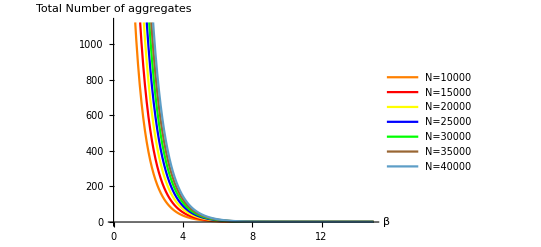

```mathematica
ListLinePlot[{(∑_(l=1)^10000 l^1.5×ⅇ^(-J05×l))/(∑_(l=1)^10000 l^2.5×ⅇ^(-J05×l))×10000,(∑_(l=1)^15000 l^1.5×ⅇ^(-J1×l))/(∑_(l=1)^15000 l^2.5×ⅇ^(-J1×l))×15000,(∑_(l=1)^20000 l^1.5×ⅇ^(-J105×l))/(∑_(l=1)^20000 l^2.5×ⅇ^(-J105×l))×20000,(∑_(l=1)^25000 l^1.5×ⅇ^(-J2×l))/(∑_(l=1)^25000 l^2.5×ⅇ^(-J2×l))×25000,(∑_(l=1)^30000 l^1.5×ⅇ^(-J205×l))/(∑_(l=1)^30000 l^2.5×ⅇ^(-J205×l))×30000,(∑_(l=1)^35000 l^1.5×ⅇ^(-J3×l))/(∑_(l=1)^35000 l^2.5×ⅇ^(-J3×l))×35000,(∑_(l=1)^40000 l^1.5×ⅇ^(-J305×l))/(∑_(l=1)^40000 l^2.5×ⅇ^(-J305×l))×40000},DataRange->{0,15},PlotStyle->{Orange,Red,Yellow,Blue,Green,Brown,Grey},PlotLegends->{"N=10000","N=15000","N=20000","N=25000","N=30000","N=35000","N=40000"},AxesLabel->{"β","Total Number of aggregates"}]
```

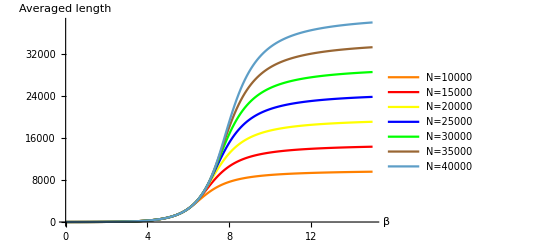

```mathematica
ListLinePlot[{(∑_(l=1)^10000 l^2.5×ⅇ^(-J05×l))/(∑_(l=1)^10000 l^1.5×ⅇ^(-J05×l)),(∑_(l=1)^15000 l^2.5×ⅇ^(-J1×l))/(∑_(l=1)^15000 l^1.5×ⅇ^(-J1×l)),(∑_(l=1)^20000 l^2.5×ⅇ^(-J105×l))/(∑_(l=1)^20000 l^1.5×ⅇ^(-J105×l)),(∑_(l=1)^25000 l^2.5×ⅇ^(-J2×l))/(∑_(l=1)^25000 l^1.5×ⅇ^(-J2×l)),(∑_(l=1)^30000 l^2.5×ⅇ^(-J205×l))/(∑_(l=1)^30000 l^1.5×ⅇ^(-J205×l)),(∑_(l=1)^35000 l^2.5×ⅇ^(-J3×l))/(∑_(l=1)^35000 l^1.5×ⅇ^(-J3×l)),(∑_(l=1)^40000 l^2.5×ⅇ^(-J305×l))/(∑_(l=1)^40000 l^1.5×ⅇ^(-J305×l))},DataRange->{0,15},PlotStyle->{Orange,Red,Yellow,Blue,Green,Brown,Grey},PlotLegends->{"N=10000","N=15000","N=20000","N=25000","N=30000","N=35000","N=40000"},AxesLabel->{"β","Averaged length"}]
```